```mathematica
ClearAll;
Clear[na];
sel[au_,kl_]:=au[[All,kl]];
(*
Comenzamos con la definicion de ferm, que genera el espacio de Fock para na SP states de un fermion (Dim(H) = 2^na estados puros). No usamos Module, ya que muchas de las definciones las usaremos por fuera del entorno de la funcion
*)
ferm[na_]:=(n=na;
Clear[cm,estado,a,v,mat,au,kel];
(*
Table es un análogo a los list comprehension, iterando con {index, start=1, end, paso=1}. IntegerDigits da una representación en base 2 de k, usando n digitos, en formato de lista. Cada uno de estos, representa un estado puro en el espacio de Fock, con cada posición en la tabla el número de ocupación del SP. De este modo, state corresponde a una base del espacio
*)
state=Table[IntegerDigits[k,2,n],{k,0,2^n-1,1}]; 
(* 
Genera una lista de 2^n elementos ceros, salvo el primero. Usa la misma indexacion que state, de modo que indica cual es el vacio del espacio de Fock en la base state
*)
vacio=Table[If[i==1,1,0],{i,Length[state]}];
(* 
Vamos a crear las matrices de destrucción y creación notadas como cm[i]->Subscript[c, i] y cdm[i]->Subscript[c, i]^†, definidas en 2^n x2^n. Para ello, creamos la funcion auxiliar c(i,m), que, dado el indice del elemento de la base (m), y el nivel SP a desocupar (i), devuelve el indice del estado m con el nivel i desocupado, o 0 si ese nivel estaba desocupado (0 ≠ vacio). Además, este índice cuenta con un signo según la paridad de los niveles ocupados previos al i.
*)
c[i_,m_]:=(st=state[[m]];If[st[[i]]==0,0,(-1)^(Tr[Take[st,i-1]])*(FromDigits[ReplacePart[st,i->0],2]+1)]);
(*
Creamos cada una de las matrices de destrucción iterando con Do sobre los niveles de ocupación (i). Para construir cada una de ellas usamos una SparseArray. Notar que las entradas dt=c[i,m]
{If[dt≠0,Abs[dt],m],m}->Sign[dt]}
Indican que el estado m debe ser enviado a Abs[c[i,m]],   con el signo dado para que las relaciones de conmutación sean las correctas (en particular, las relativas al intercambio de dos fermiones). También creamos los op de creacion, trasponiendo los de destrucción
*)
Do[cm[i]=SparseArray[Join[Table[{m,m}->0,{m,Length[state]}],Table[{dt=c[i,m];If[dt≠0,Abs[dt],m],m}->Sign[dt],{m,Length[state]}]]];
cdm[i]=Transpose[cm[i]],{i,n}]; 
(* Generamos los operadores producto Subscript[c, i]^†Subscript[c, j] Subscript[c, i] Subscript[c, j]^† Subscript[c, i] Subscript[c, j] Subscript[c, i]^†Subscript[c, j]^† *)
Do[cdcm[i,j]=cdm[i].cm[j];ccdm[i,j]=cm[i].cdm[j];ccm[i,j]=cm[i].cm[j];cdcd[i,j]=cdm[i].cdm[j],{i,n},{j,n}]; 
(* 
A continuacion, definimos algunas funciones auxiliares
 *) 
 mf[au_]:=MatrixForm[au]; (* Atajo de MatrixForm *)
indx[au_]:=Flatten[SparseArray[au]["NonzeroPositions"],1];
(* Indica las posiciones de los elementos no nulos de un vector au *)
Do[statex[kel]=Select[state,Tr[#]==kel&];leme[kel]=Length[statex[kel]],{kel,0,n,1}];
(* Selecciona estados con kel fermiones para todo kel (kel es el numero de fermiones), almacenado en statex. Mientras que leme[kel] devuelve en numero de estados con esa cantidad de fermiones *) 
Clear[i,j,m,nuu,au];
(*
Vamos a ver ahora las descomposiciones bipartitas de los estados. Estos corresponden a la matrix Γ del paper definida en la ec 9. i corresponde al índice en el espacio de estados de m fermiones, y j al mismo en nuu-m. au es el estado a descomponer. 
Para la eleccion i,j, si creo un estado no nulo (ax.ay==0), tomo el coeficiente de au asociado a ese estado. Adicionalmente, le pongo un signo para BD.
nuu corresponde al numero de particulas, y au el estado a descomponer
*)
cof[i_,j_,m_,nuu_,au_]:=(ax=statex[m][[i]];axi=indx[ax];ay=statex[nuu-m][[j]];
If[ax.ay==0,au[[iex=FromDigits[ax+ay,2]+1]]*(-1)^(Sum[Tr[Take[ay,axi[[ki]]-1]],{ki,Length[axi]}]),0]);
(* Con los coef de Γ, calculamos la matrix de M cuerpos *)
rhomc[m_,nuu_,au_]:= Table[Sum[cof[i,k,m,nuu,au]Conjugate[cof[j,k,m,nuu,au]],{k,leme[nuu-m]}],{i,leme[m]},{j, leme[m]}];
rho1c[v_]:=Table[v.cdcm[j,i].v,{i,n},{j,n}];
(* Calcula la matriz densidad de un cuerpo en el estado v*) 
num=Sum[cdcm[i,i],{i,n}]);

(* operador numero de fermiones *)
ssp[mat_]:=(zp=Eigenvalues[mat];a=Select[zp,#>0&&#<1&];If[Length[a]>0,-(a.Log[a]+(1-a).Log[1-a])/Log[2],0]);
(* Calcula la entropia fermionica de una matriz densidad de un cuerpo mat *)  
rev[au_]:=(let=Length[au];
Table[au[[let-i+1,let-j+1]],{i,let},{j,let}]);
(* reversa del orden de estados *)
```

### Ejemplos

```mathematica
ferm[8];
estat=cdm[1].cdm[2].cdm[3].cdm[4].vacio;
{estat.estat,estat.num.estat,estat}
 m=2;nume=4;
rhomc[m, nume, estat] // mf
m=2; nume=4;cmat=Table[cof[i,j,m,nume,estat],{i,leme[m]},{j,leme[nume-m]}];cmatt=rev[cmat.Transpose[cmat]];cmatt//mf
```

{1,4,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

## Hamiltoniano de Pairing

Apliquemos ahora el formalismo anterior para estudiar las descomposiciones y matrices de M cuerpos para estados un poco más interesantes. En este caso, evaluaremos los autoestados del hamiltoniano de Pairing. El mismo, consiste en un término de niveles discretos con degeneración dos (por ejemplo, k y k’), junto con otro término que acopla estos dos niveles, reduciendo la energía. De este modo, esperamos que en el fundamental los estados se den únicamente de a pares. Estudiaremos sistemas de 2n estados y n fermiones (porque es donde se da la física más interesante). Construimos el hamiltoniano para n fermiones:

```mathematica
pairing[n_]:=(nn=n;
it=0;
Clear[xst,xstt,indax];
(* Al igual que en ferm, vamos a representar estados usando vectores binarios, que indican los niveles ocupados. En este
caso, vamos a notarlos como (Subscript[k, 1],Subscript[k, 1]'...), de modo que únicamente nos quedamos con los estados con ambas degeneraciones ocupadas,
ya que esperamos que solo estos contribuyan al fudamental. Más aún, para reducir la dimension del espacio, colapsamos la degeneracion, notando los estados como (Subscript[k, 1],Subscript[k, 2]...=(Subscript[k, 1],Subscript[k, 1]',Subscript[k, 2],Subscript[k, 2]'... *)
(* Construimos los estados al igual que en ferm, y nos quedamos unicamente con los estados con n/2 fermiones, ie, estados = statex[n/2]*)
Table[xstate=IntegerDigits[k,2,nn];If[Tr[xstate]==nn/2,it=it+1;xst[it]=xstate;indax[xstate]=it],{k,0,2^nn-1,1}];
itm=it;
Do[xstl[l]=Table[xst[k][[l]],{k,itm}],{l,nn}];
estados=Table[xst[it],{it,itm}];
(* Construimos la parte de la energia de cada nivel *)
e=1.;
e0=e*Table[k-nn/2-1/2,{k,nn}]; (* Energia de cada modo *)
h0=Table[e0.estados[[i]],{i,itm}]; (* Energia de cada estado *)
h00=DiagonalMatrix[h0]; (* Primera parte del Hamiltoniano *)
(* Ahora vamos a construir el término de interacción. Como la constante es la misma, y estamos sumando sobre todos los operadores,
esta simplemente aporta un término G por cada par de estados que difieren en un modo (es decir, que se obtienen via intercambio de las ocupaciones de k <-> k' *)
Clear[g];
hi=Table[If[estados[[i]].estados[[j]]==nn/2-1,g,0],{i,itm},{j,itm}];
h=h00+hi;
(* Definamos ahora una funcion que nos permite pasar de los estados de esta convencion, a la de ferm.
Primero definimos una funcion auxiliar que asigna a que elemento de la base reducida corresponde a la nueva *)
convelem[au_]:=Module[{s=au,x},
x =Table[0,{i,2Length[s]}];
Do[x[[2i-1]]=s[[i]];
    x[[2i]]=s[[i]];,{i,Length[s]}];
x];
conv[au_]:=Module[{s=au, newCor},
state =Table[IntegerDigits[k,2,2 n],{k,0,2^(2n)-1,1}];
newCor = Table[0,{i,Length[state]}];
Do[idx=Position[state,convelem[estados[[k]]]][[1,1]];
newCor[[idx]]=s[[k]],{k,Length[s]}];
newCor];
)
```

Nos interesa ver el comportamiento de los autovalores de la matriz de M cuerpos, para distintos niveles de energía de h (fundamental, primer excitado...) haciendo un barrido en g. Hasta ahora, con pairing, teníamos definido h

```mathematica
d= 8; (* Dimension del espacio, d | 4 *)
M = 2; (* Grado de la descomposicion, donde 0≤M≤d/2 *)
(* Parametros del barrido *)
gmin = 0.1;
gmax = 0.2;
gstep = 0.1;
ferm[d];
pairing[d/2];
(* Calculamos autovals y autovect de H, y ordenamos de acuerdo al autovalor. El resultado es una lista de la forma
{{autoval,autovect},...}. Como este fue calculado en un subespacio, lo convertimos al espacio original, y finalmente,
calculamos los autovalores de rho *)
eigenTab =ParallelTable[
{evals,evecs}=Eigensystem[h];
a=SortBy[Transpose[{evals,evecs}],First];
(* El primer indice de a corresponde al nivel, 1 = fundamental, 2 = 1er excitado... 
Adicionalmente, lo convertimos a la base de ferm *)
targState = conv[a[[1]][[2]]];
(* Calculamos los autovalores de la rhom *)
rhomEvals = Timing[Eigenvalues[rhomc[M,d/2,targState]]],
{g,gmin,gmax,gstep}]
```

Syntax::sntxf: "{evals,evecs}=Eigensystem[h];a=SortBy[Transpose[{evals,evecs}],First];targState=conv[a[[1]][[2]]];" cannot be followed by "rhomEvals=Timing[Eigenvalues[rhomc[M,d/2,targState]]],{g,gmin,gmax,gstep}".

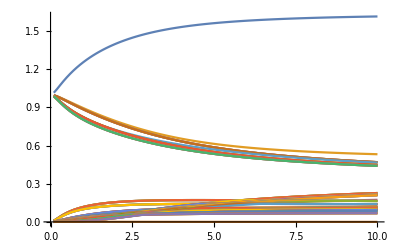

```mathematica
ListLinePlot[Transpose[eigenTab],DataRange->{gmin,gmax},PlotRange->All]
```

```mathematica
d= 12; (* Dimension del espacio, d | 4 *)
M = 2; (* Grado de la descomposicion, donde 0≤M≤d/2 *)
(* Parametros del barrido *)
gmin = 0.1;
gmax = 0.2;
gstep = 0.1;
ferm[d];
pairing[d/2];
(* Calculamos autovals y autovect de H, y ordenamos de acuerdo al autovalor. El resultado es una lista de la forma
{{autoval,autovect},...}. Como este fue calculado en un subespacio, lo convertimos al espacio original, y finalmente,
calculamos los autovalores de rho *)
g=0.1;
{evals,evecs}=Eigensystem[h]
a=SortBy[Transpose[{evals,evecs}],First];
(* El primer indice de a corresponde al nivel, 1 = fundamental, 2 = 1er excitado... 
Adicionalmente, lo convertimos a la base de ferm *)
targState = conv[a[[1]][[2]]];
(* Calculamos los autovalores de la rhom *)
rhomEvals = Timing[Eigenvalues[rhomc[M,d/2,targState]]]
```

{{4.54411,-4.53151,-3.52965,3.52881,-2.52304,-2.52304,2.52225,2.52225,-1.52005,1.51424,1.51424,1.50922,-1.50791,-1.50791,-0.508978,0.508046,-0.505674,-0.505674,0.500137,0.500137},{{-0.986075,-0.115721,-0.0600409,-0.0403227,-0.0600409,-0.038712,-0.0286797,-0.00720472,-0.00518671,-0.00305232,-0.0403227,-0.0286797,-0.022487,-0.00518671,-0.00387656,-0.00235137,-0.00305232,-0.00235137,-0.00161286,-0.000374552},{-0.000234451,0.00105081,0.00142887,0.00181864,0.00142887,0.00245512,0.00328064,-0.0178905,-0.0219438,-0.0275903,0.00181864,0.00328064,0.00461225,-0.0219438,-0.0288781,-0.0414173,-0.0275903,-0.0414173,-0.0841947,0.992865},{0.000876979,-0.00036348,0.00284616,0.00347296,0.00284616,-0.017095,-0.0201199,0.000630381,0.00247477,-0.0460883,0.00347296,-0.0201199,-0.0253583,0.00247477,0.00645625,-0.095402,-0.0460883,-0.095402,0.985034,0.0735911},{0.131462,-0.977511,-0.0954304,-0.0494799,-0.0954304,-0.00560613,-0.00188748,-0.0410814,-0.0297322,-0.00454896,-0.0494799,-0.00188748,-0.0000310499,-0.0297322,-0.0227596,-0.00341682,-0.00454896,-0.00341682,-0.00038531,-0.00173901},{0.00197568,0.00345055,-0.00920997,-0.00598184,-0.0130372,0.00230894,-0.0245765,0.00541152,-0.031251,-0.0652931,-0.0118852,-0.0160099,-0.0638117,-0.0182297,-0.12562,0.554988,-0.0903833,0.799814,0.118233,0.0580523},{0.000350013,0.000611302,-0.0127723,-0.0182438,0.00883097,0.000409054,0.0205822,0.00095871,0.0323669,-0.0846019,0.0150785,-0.0277726,-0.0113049,-0.0411329,-0.022255,0.81098,0.0570221,-0.570962,0.0209463,0.0102846},{-0.0770664,-0.151835,0.81354,0.0680553,0.519973,0.143693,0.0359479,0.0705954,0.0194941,0.0293276,0.0401371,0.0495107,0.00516245,0.028713,0.00113552,0.0199863,0.0217271,0.0129801,0.00533547,0.00298045},{0.0164682,0.0324454,0.544429,0.0537649,-0.829385,-0.0307054,-0.0408659,-0.0150854,-0.0267216,0.0123292,-0.0768843,0.0226044,-0.00110315,0.0164203,-0.000242647,0.0128712,-0.023239,-0.0199158,-0.00114013,-0.000636886},{0.00264528,-0.0145315,0.00138141,-0.0275255,0.00138141,-0.000563667,0.00801098,0.0102215,-0.103273,-0.00927083,-0.0275255,0.00801098,-0.107886,-0.103273,0.975454,0.0787534,-0.00927083,0.0787534,0.00391311,0.0309404},{0.00183277,0.00260745,0.0651066,-0.724776,-0.0594168,0.000644463,-0.0830964,0.000399859,-0.0437105,-0.0265438,0.669889,0.077432,-0.00311327,0.0408906,-0.00199416,-0.0142835,0.0246161,0.0125253,-0.000238476,-0.000138645},{0.0462138,0.0657475,0.0692647,-0.664328,0.0742031,0.0162503,-0.0682322,0.0100825,-0.0338735,-0.0232888,-0.719639,-0.0745985,-0.0785018,-0.0372287,-0.0502831,-0.0216348,-0.0253177,-0.022698,-0.00601323,-0.00349596},{0.0304267,-0.00976054,0.116174,0.0116683,0.116174,-0.972799,-0.087864,-0.0824507,-0.00454513,-0.0348387,0.0116683,-0.087864,-0.00739193,-0.00454513,-0.000258012,-0.000866616,-0.0348387,-0.000866616,-0.0245638,-0.00312476},{0.000437294,0.000784171,-0.0226648,-0.0249338,0.0187892,-0.00622291,-0.0326839,-0.00882144,-0.0679283,0.791612,0.0189112,0.0229375,-0.00118896,0.0489563,-0.00201625,0.0836343,-0.592827,-0.0647032,0.0104004,0.0066277},{-0.00302537,-0.0054252,0.0104104,0.0176647,0.0164023,0.0430525,0.0296946,0.0610301,0.0571803,-0.58758,0.0240021,0.0377343,0.00822567,0.0740751,0.0139492,-0.0547658,-0.78769,-0.0762069,-0.0719539,-0.0458529},{0.0140293,-0.000786239,-0.00402565,0.0497091,-0.00402565,-0.00914757,0.0979283,-0.00141481,0.0120631,0.00639488,0.0497091,0.0979283,-0.980016,0.0120631,-0.0965876,-0.0476452,0.00639488,-0.0476452,-0.0294369,-0.00465579},{0.00673103,-0.0359313,-0.049302,-0.00633777,-0.049302,-0.0966409,-0.0117536,0.980186,0.0953838,0.0468522,-0.00633777,-0.0117536,-0.00134067,0.0953838,0.00864327,0.00358504,0.0468522,0.00358504,0.000123666,0.0255707},{-0.00583415,0.0312769,0.0155771,0.0405732,0.0178653,-0.0105419,0.0752879,0.1443,-0.721123,-0.0536502,0.0368908,0.067344,0.0177654,-0.64485,-0.13625,-0.0368148,-0.0472377,-0.0399893,-0.00221542,-0.0385004},{0.00031871,-0.00170861,-0.0218563,0.0315877,0.0200294,0.000575887,0.0688131,-0.00788285,-0.660803,-0.0559361,-0.0358194,-0.0766048,-0.000970493,0.735424,0.00744312,0.0311539,0.0614474,-0.0269583,0.000121025,0.00210321},{0.0282779,-0.00474708,0.0256077,0.0908762,0.0281531,0.136122,-0.704765,0.015527,-0.0644191,-0.0285047,0.0859136,-0.662137,-0.126102,-0.0605391,-0.0069915,-0.0269947,-0.0263783,-0.0285545,-0.0368134,-0.00527322},{-0.000865126,0.000145231,-0.0424215,0.0784005,0.0407768,-0.00416447,-0.675758,-0.000475028,-0.0615007,-0.0339121,-0.0838091,0.717577,0.00385791,0.0653236,0.000213896,0.026343,0.0355912,-0.0246436,0.00112626,0.000161327}}}

{54.2396,{1.01522,0.995923,0.995346,0.995346,0.995346,0.995346,0.988811,0.988811,0.988811,0.988811,0.988765,0.987343,0.987343,0.987343,0.987343,0.00883618,0.00883618,0.00883618,0.00883618,0.00786676,0.00786676,0.00786676,0.00786676,0.00257392,0.00257392,0.00257392,0.00257392,0.00248197,0.00248197,0.00248197,0.00248197,0.00220973,0.00220973,0.00220973,0.00220973,0.00131989,0.00131989,0.00131989,0.00131989,0.00125682,0.00125682,0.00125682,0.00125682,0.00108936,0.00108936,0.00108936,0.00108936,0.000804745,0.000804745,0.000804745,0.000804745,0.0000765286,0.0000353979,0.0000353979,0.0000353979,0.0000353979,0.0000188869,0.0000188869,0.0000188869,0.0000188869,0.0000106123,6.50827×10^-6,6.50827×10^-6,6.50827×10^-6,6.50827×10^-6,3.01644×10^-6}}